## Final Boat Calculations

```mathematica
boatFunc[n_?NumberQ,d_?NumberQ,xVal_]:=Exp[Abs[y/(n*(xVal^2-4))]]+(xVal^2-4)/6≤z≤d
```

```mathematica
mass[n_?NumberQ,d_?NumberQ]:=mass[n,d]=NIntegrate[1/4,{x,y,z}∈ImplicitRegion[boatFunc[n,d,x],{x,y,z}],AccuracyGoal->5]
massApprox[n_?NumberQ,d_?NumberQ,freq_?NumberQ]:=massApprox[n,d,freq]=freq*Total[NIntegrate[1/4,{y,z}∈ImplicitRegion[boatFunc[n,d,#],{y,z}],AccuracyGoal->5]&/@Range[-1.99,1.99,freq]]
comY[n_?NumberQ,d_?NumberQ,freq_?NumberQ]:=(freq*Total[NIntegrate[y/4,{y,z}∈ImplicitRegion[boatFunc[n,d,#],{y,z}],AccuracyGoal->5]&/@Range[-1.999,(1.999-freq),freq]])/massApprox[n,d,freq]
comZ[n_?NumberQ,d_?NumberQ,freq_?NumberQ]:=(freq*Total[NIntegrate[z/4,{y,z}∈ImplicitRegion[boatFunc[n,d,#],{y,z}],AccuracyGoal->5]&/@Range[-1.999,(1.999-freq),freq]])/massApprox[n,d,freq]
```

```mathematica
mass[.4,1]//AbsoluteTiming
```

{2.18803×10^-6,0.23095}

```mathematica
massOfWater[.4,1,0,.5]//AbsoluteTiming
```

```mathematica
comZ[.5,1,.1]
```

0.795277

```mathematica
comY[.4,1,.5]//AbsoluteTiming
```

{1.17493,0.}

```mathematica
ClearAll[findB]
```

```mathematica
water[theta_, b_] := If[theta==π/2,0≤y≤2&&0≤z≤2,If[theta<π/2,z≤Tan[theta]*y+b,z≥Tan[theta]*y+b]]
submergedRegion[n_?NumberQ,d_?NumberQ,xVal_,theta_,b_] := boatFunc[n,d,xVal] && water[theta,b]
massOfWater[n_?NumberQ,d_?NumberQ,theta_,b_]:=NIntegrate[1,{x,y,z}∈ImplicitRegion[submergedRegion[n,d,x,theta,b],{x,y,z}],AccuracyGoal->5]
findB[n_,d_,theta_] :=findB[n,d,theta]=FindRoot[mass[n,d]-massOfWater[n,d,theta,b]==0,{b,.5},AccuracyGoal->3,PrecisionGoal->6]
```

```mathematica
findB[.45,1,0]//AbsoluteTiming
```

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region ImplicitRegion[«2»].

{26.0403,{b→0.701387}}

```mathematica
findB[.4,1,0]//AbsoluteTiming
```

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region ImplicitRegion[«2»].

{25.8231,{b→0.705573}}

```mathematica
b/.findB[.6,1,0]
```

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region ImplicitRegion[«2»].

```mathematica
cobY[n_?NumberQ,d_?NumberQ,theta_?NumberQ]:=NIntegrate[y,{x,y,z}∈ImplicitRegion[submergedRegion[.4,1,x,0,b/.findB[n,d,theta]],{x,y,z}],AccuracyGoal->5]/massOfWater[n,d,theta,b/.findB[n,d,theta]]
cobZ[n_?NumberQ,d_?NumberQ,theta_?NumberQ]:=NIntegrate[z,{x,y,z}∈ImplicitRegion[submergedRegion[.4,1,x,0,b/.findB[n,d,theta]],{x,y,z}],AccuracyGoal->5]/massOfWater[n,d,theta,b/.findB[n,d,theta]]
```

```mathematica
buoyForce[n_,d_]:=mass[n,d]*(9.81)
momentArm[n_,d_,theta_]:={0,cobY[n,d,theta]-comY[n,d,.25],cobZ[n,d,theta]-comZ[n,d,.25]}
moment[n_,d_,theta_]:=momentArm[n,d,theta]×{buoyForce[n,d]*-Sin[theta],buoyForce[n,d]*Cos[theta],0}
```

```mathematica
moment[.4,1,0]//AbsoluteTiming
moment[.4,1,.1]//AbsoluteTiming
moment[.4,1,.2]//AbsoluteTiming
moment[.4,1,.3]//AbsoluteTiming
```

ImplicitRegion::msgs: Evaluation of {submergedRegion[0.4,1,x,0,b/.findB[0.4,1,0]],True} generated message(s) {DiscretizeRegion::drf}.

{38.8256,{0.473825,0.,0.}}

ImplicitRegion::msgs: Evaluation of {submergedRegion[0.4,1,x,0,b/.findB[0.4,1,0.1]],True} generated message(s) {DiscretizeRegion::drf}.

{129.169,{0.631127,0.0633239,0.}}

$Aborted

```mathematica
Map[moment[.4,1,#]&,{0,.1,.2,.3}]//AbsoluteTiming
```

ImplicitRegion::msgs: Evaluation of {submergedRegion[0.4,1,x,0,b/.findB[0.4,1,0.2]],True} generated message(s) {DiscretizeRegion::drf}.

```mathematica
ParallelMap[moment[.4,1,#]&,{0,.1,.2,.3}]//AbsoluteTiming
```

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region ImplicitRegion[«2»].

General::stop: Further output of DiscretizeRegion::drf will be suppressed during this calculation.

ImplicitRegion::msgs: Evaluation of {submergedRegion[0.4,1,x,0,b/.findB[0.4,1,0.1]],True} generated message(s) {DiscretizeRegion::drf}.

$Aborted

{0.,0.5,1.,1.5,2.,2.5,3.}

{{0.473825,0.,0.},{0.863547,0.471758,0.},{0.604257,0.941074,0.},{0.0802151,1.13115,0.},{-0.475326,1.03861,0.},{-0.959343,0.716651,0.},{-1.31068,0.186833,0.}}

{0.473825,0.863547,0.604257,0.0802151,-0.475326,-0.959343,-1.31068}

{{0.,0.473825},{0.5,0.863547},{1.,0.604257},{1.5,0.0802151},{2.,-0.475326},{2.5,-0.959343},{3.,-1.31068}}

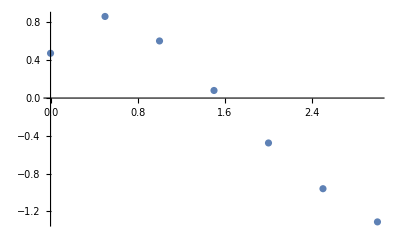

```mathematica
angles = Range[0,π,.5]
momentPoints = ParallelMap[moment[.4,1,#]&,angles]
moments = momentPoints[[All,1]]
points = Transpose[{angles,moments}]
ListPlot[points,Axes->True,AxesLabel->Automatic,Frame->None]
```

```mathematica
RegionPlot3D[submergedRegion[.4,1,x,N[π/6],.7],{x,-1.99,1.99},{y,-2,2},{z,0,2}]
```

-Graphics3D-

```mathematica
massOfWater[.4,1,0,.7,.1]
```

0.225397